```mathematica
<<Units`
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
f[θ_]:=k-k/(1+(k (1-Cos[θ]))/me)
dσdΩ=α^2/me^2 P^2/2(P+1/P-Sin[θ]^2)/.P->1/(1+k/me(1-Cos[θ]));
comptontrial=1/(3 k^2 me (2 k+me)^3)π α^2 (2 k (-10 k^4+51 k^3 me+93 k^2 me^2+51 k me^3+9 me^4)+3 (2 k+me)^3 (k^2-2 k me-3 me^2) Log[-2 k-me]-3 (2 k+me)^3 (k^2-2 k me-3 me^2) Log[-me]);
comptontest=LogLogPlot[n comptontrial(5.*^5)/.{me->0.5,α->1/137,n->8},{k,10^-1,10^10},PlotStyle->Dashed];
```

#### With Pauli-Blocking:

```mathematica
α^2/me^2 P^2/2(P+1/P-Sin[θ]^2)/.P->1/(1+k/me(1-Cos[θ]))/.Cos[θ]->x
```

(α^2 (1+1/(1+(k (1-x))/me)+(k (1-x))/me-Sin[θ]^2))/(2 me^2 (1+(k (1-x))/me)^2)

```mathematica
ff[x_]:=f[θ]/.Cos[θ]->x
dσdx=(α^2 (1+1/(1+(k (1-x))/me)+(k (1-x))/me-(1-x^2)))/(2 me^2 (1+(k (1-x))/me)^2)*2Pi;
comptonpauli=Integrate[dσdx*ff[x]*n ff[x]/Ef,x];
comptonnon=Integrate[dσdx*ff[x]n,x];
Solve[ff[x]==Ef,x]//FullSimplify
```

{{x→1+(Ef me)/((Ef-k) k)}}

```mathematica
pauli1=comptonpauli/.x->1+(Ef me)/((Ef-k) k);
pauli2=comptonpauli/.x->1;
pauli1non=comptonnon/.x->-1;
pauli2non=comptonnon/.x->1+(Ef me)/((Ef-k) k);
comptontot=(pauli1-pauli2)+(pauli1non-pauli2non)//Simplify;
```

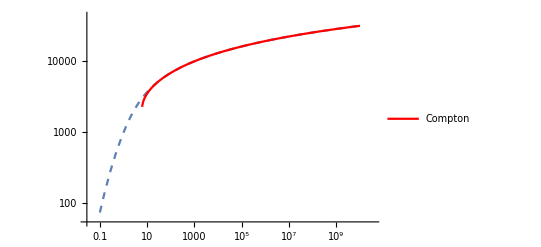

```mathematica
compton=LogLogPlot[ReplaceAll[-comptontot(5.*^5)/.{me->0.5,α->1/137,Ef->(3 Pi^2 n)^(1/3)},n->8],{k,10^-2,10^10},PlotLegends->{"Compton"},PlotStyle->{Red,Thick}];
compton2=LogLogPlot[ReplaceAll[-comptontot(5.*^5)/.{me->0.5,α->1/137,Ef->(3 Pi^2 n)^(1/3)},n->0.08],{k,10^-2,10^10},PlotLegends->{"Compton"},PlotStyle->{Red,Thick}];
Show[comptontest,compton]
```

#### Full Klein-Nishina scattering cross section (averaged over scattering angles) - k=ω/m_e

```mathematica
σ=2Pi α^2/me^2((1+k)/k^2((2(1+k))/(1+2k)-Log[1+2k]/k)+Log[1+2k]/(2k)-(1+3k)/(1+2k)^2);
```

#### Two limits:

```mathematica
Normal[Series[σ,{k,0,0}]]
```

(8 π α^2)/(3 me^2)

```mathematica
FullSimplify[Normal[Series[σ/.k->1/x,{x,0,1}]]/.x->me/ω]
```

(π α^2 (1+Log[4]-2 Log[me/ω]))/(2 me ω)